```mathematica
NumS = s^2+Subscript[ω, c]^2;
DenS = s^2+Δω s + Subscript[ω, c]^2;
```

```mathematica
G = TransferFunctionModel[NumS/DenS,s]
```

(s^2+ω_c^2)/(Δω s+s^2+ω_c^2)

```mathematica
Gd = ToDiscreteTimeModel[G,T, z,Method->{"BilinearTransform","CriticalFrequency"->Subscript[ω, c]}]
```

(2 (1+z^2-2 z Cos[T ω_c]) ω_c)/(-Δω Sin[T ω_c]+Δω z^2 Sin[T ω_c]+2 ω_c+2 z^2 ω_c-4 z Cos[T ω_c] ω_c)T

```mathematica
ZeroS =Flatten@Solve[{NumS== 0},s]
```

{s→-ⅈ ω_c,s→ⅈ ω_c}

```mathematica
PoleS = Simplify[ComplexExpand@Flatten@Solve[{DenS== 0},s],Δω^2-4 Subscript[ω, c]^2 < 0]
```

{s→1/2 (-Δω-ⅈ √(-Δω^2+4 ω_c^2)),s→1/2 ⅈ (ⅈ Δω+√(-Δω^2+4 ω_c^2))}

```mathematica
ZeroZ1 = FullSimplify@Exp[T s/.ZeroS⟦1⟧]
```

ⅇ^(-ⅈ T ω_c)

```mathematica
ZeroZ2 = FullSimplify@Exp[T s/.ZeroS⟦2⟧]
```

ⅇ^(ⅈ T ω_c)

```mathematica
PoleZ1 = FullSimplify@Exp[T s/.PoleS⟦1⟧]
```

ⅇ^(-1/2 ⅈ T (-ⅈ Δω+√(-Δω^2+4 ω_c^2)))

```mathematica
PoleZ2 = FullSimplify@Exp[T s/.PoleS⟦2⟧]
```

ⅇ^(1/2 ⅈ T (ⅈ Δω+√(-Δω^2+4 ω_c^2)))

```mathematica
NumZ =FullSimplify[Expand[ (z-ZeroZ1)(z-ZeroZ2)]]
```

1+z^2-2 z Cos[T ω_c]

```mathematica
DenZ = FullSimplify[ComplexExpand[(z-PoleZ1)(z-PoleZ2)],Δω^2-4 Subscript[ω, c]^2 < 0]
```

ⅇ^(-T Δω)+z^2-2 ⅇ^(-(T Δω)/2) z Cos[1/2 T √(-Δω^2+4 ω_c^2)]

```mathematica
CoefficientList[NumZ,z]
```

{1,-2 Cos[T ω_c],1}

```mathematica
CoefficientList[DenZ,z]
```

{ⅇ^(-T Δω),-2 ⅇ^(-(T Δω)/2) Cos[1/2 T √(-Δω^2+4 ω_c^2)],1}

```mathematica
Gz =(k NumZ)/(z^2+a z + b)
```

(k (1+z^2-2 z Cos[T ω_c]))/(b+a z+z^2)

```mathematica
Solve[(Gz/.z->1)== 1,k]
```

{{k→-(1+a+b)/(2 (-1+Cos[T ω_c]))}}

```mathematica
Exp[1.0 π]
```

23.1407

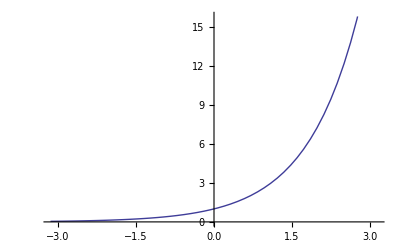

```mathematica
Plot[Exp[x],{x,-π,π}]
```